# Hexagon

### Author

Eric W. Weisstein
July 3, 2018

This notebook downloaded from http://mathworld.wolfram.com/notebooks/Polygons/Hexagon.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/Hexagon.html.

©2018 Wolfram Research, Inc. except for portions noted otherwise

## Examples

```mathematica
laminae=Select[EntityList[EntityClass["Lamina","Polygon"]],#["VertexCount"]==6&]
```

{regular hexagon,rectangular L-beam,square L-beam}

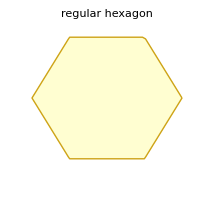
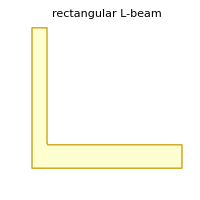
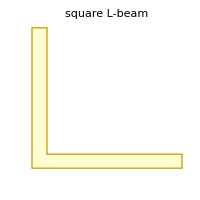

```mathematica
Show[#,PlotLabel->#2]&@@@EntityValue[laminae,{"Graphics","Name"}]
```

## Figure

```mathematica
polys={
Polygon[Entity["Lamina","FilledRegularHexagon"]["Vertices"][1]]->"regular hexagon",
Polygon[{#,1.3#2}&@@@(Entity["Lamina","FilledRegularHexagon"]["Vertices"][1][[1]])]->"squashed hexagon",
Polygon[Entity["Lamina","SquareLBeam"]["Vertices"][1,.3]]->"square L-beam",
{Polygon[CirclePoints[{1,3π/2},3]],Polygon[CirclePoints[3]]}->"hexagram",
Polygon[{{-1,-1},{-1,1},{0,-1},{1,1},{1,-1},{0,1}}]->"butterfly hexagon",
{Polygon[CirclePoints[.5,3]],Polygon[CirclePoints[3]]}->"triangular annulus"
};
```

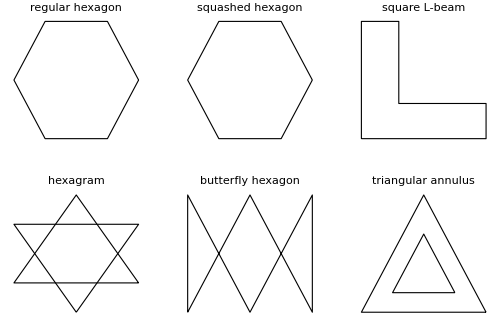

```mathematica
GraphicsGrid[Partition[
Graphics[{EdgeForm[Black],FaceForm[None],#},PlotLabel->Style[TextCell[#2,PageWidth->100,PageWidth->100],Directive[Italic,FontFamily->"Times"]]]&@@@polys,UpTo[3]],Spacings->50,ImageSize->500]
```